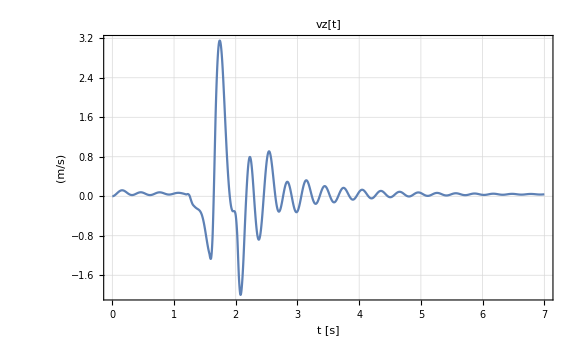

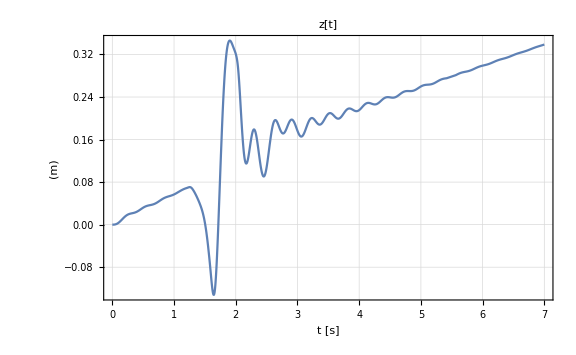

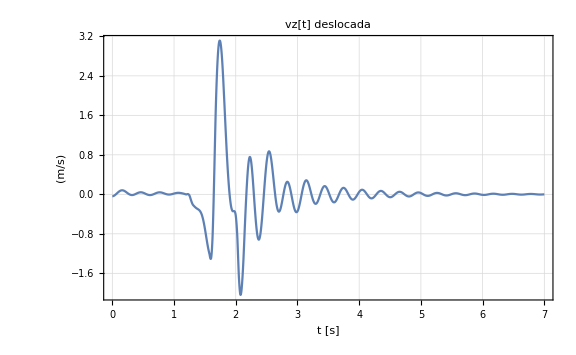

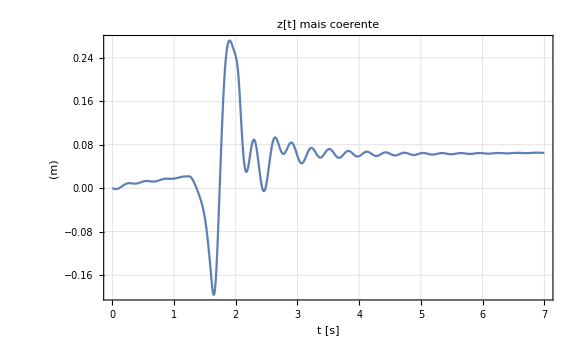

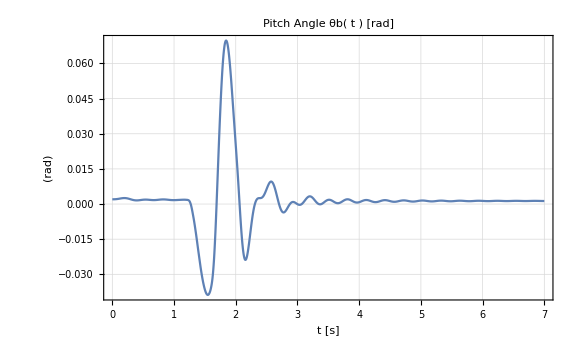

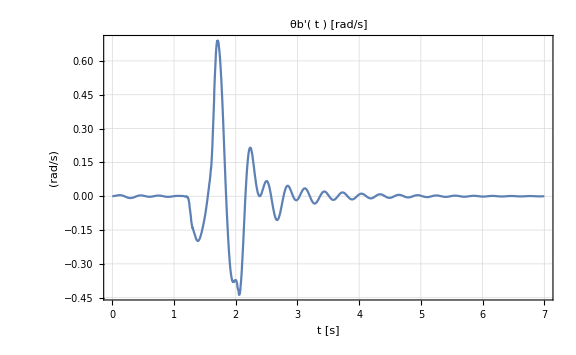

```mathematica
f=OpenRead["D:\OneDrive\Documents\POLI\IC\mecanismo e entradas\dataVz.txt"];
data1=ReadList[f,{Number,Number}];
Close[f];
a=OpenRead["D:\OneDrive\Documents\POLI\IC\mecanismo e entradas\data_Pitch_Angle.txt"];
data3=ReadList[a,{Number,Number}];
Close[a];
(* Deslocamento de dados da velocidade para que a integral (deslocamento) seja mais coerente *)
data2 =Subtract[data1,{{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083}}];


(* Transformação de grau(°) para radianos *)
data4 = Times[data3, {{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)}}];

velocidade1= Interpolation[data1];
vz= Interpolation[data2];
u1[t] = Integrate[velocidade1[t],t];
dz[t] =Integrate[vz[t],t];

angle = Interpolation[data4];
omega[t] = D[angle[t],t];

Plot[velocidade1[t],{t, 0, 7},PlotRange->{All, All}, ImageSize->Large,PlotLabel->"vz[t]",Frame->True, LabelStyle->"Subsection",GridLines->Automatic, AxesLabel->{"t [s]","(m/s)"}]
Plot[u1[t],{t, 0, 7},PlotRange->{All, All}, ImageSize->Large, PlotLabel->"z[t]",Frame->True, LabelStyle->"Subsection",GridLines->Automatic, AxesLabel->{"t [s]","(m)"}]

Plot[vz[t],{t, 0, 7},PlotRange->{All, All}, ImageSize->Large, PlotLabel->"vz[t] deslocada",Frame->True, LabelStyle->"Subsection",GridLines->Automatic, AxesLabel->{"t [s]","(m/s)"}]
Plot[dz[t],{t, 0, 7},PlotRange->{All, All}, ImageSize->Large, PlotLabel->"z[t] mais coerente",Frame->True, LabelStyle->"Subsection",GridLines->Automatic, AxesLabel->{"t [s]","(m)"}]


Plot[angle[t],{t, 0, 7},PlotRange->{All, All}, ImageSize->Large, PlotLabel->"Pitch Angle θb( t ) [rad]",Frame->True, LabelStyle->"Subsection",GridLines->Automatic, AxesLabel->{"t [s]","(rad)"}]
Plot[omega[t] ,{t, 0, 7},PlotRange->{All, All}, ImageSize->Large, PlotLabel->"θb'( t ) [rad/s]",Frame->True, LabelStyle->"Subsection",GridLines->Automatic, AxesLabel->{"t [s]","(rad/s)"}]
```

```mathematica
(* Termos de Energia *) 
T = 1/2 m ( x'[t]^2+ 1/3 L^2 θ'[t]^2);
V = m*g *x[t]  + 1/2 k ((x[t] + L Sin[θ[t]] - udir[t] - 0.5)^2 +(L(1-Cos[θ[t]])-hudir[t])^2) + 1/2 k ((x[t] - L Sin[θ[t]] - uesq[t] - 0.5)^2+(L(1-Cos[θ[t]])-huesq[t])^2);
R =  1/2 b (D[x[t] + L Sin[θ[t]] - udir[t],t]^2 +D[L(1-Cos[θ[t]]-hudir[t]),t]^2)+ 1/2 b (D[x[t] - L Sin[θ[t]] uesq[t],t]^2+D[L(1-Cos[θ[t]]-huesq[t]),t]^2);
```

```mathematica
(* Lagrange *) 
𝕢[t_] = {x[t], θ[t]};
𝕖[t_] = (D[D[T,D[#,t]],t]-D[T,#]+D[V,#]+D[R,D[#,t]]==0)& /@ 𝕢[t];
𝕖[t]//TableForm
```

g m+k (-0.5+L Sin[θ[t]]-udir[t]+x[t])+k (-0.5-L Sin[θ[t]]-uesq[t]+x[t])+b (-udir'[t]+x'[t]+L Cos[θ[t]] θ'[t])+b (-L Sin[θ[t]] uesq'[t]+x'[t]-L Cos[θ[t]] uesq[t] θ'[t])+m x''[t]==0
1/2 k (2 L (L (1-Cos[θ[t]])-hudir[t]) Sin[θ[t]]+2 L Cos[θ[t]] (-0.5+L Sin[θ[t]]-udir[t]+x[t]))+1/2 k (2 L (L (1-Cos[θ[t]])-huesq[t]) Sin[θ[t]]-2 L Cos[θ[t]] (-0.5-L Sin[θ[t]]-uesq[t]+x[t]))+1/2 b (2 L Cos[θ[t]] (-udir'[t]+x'[t]+L Cos[θ[t]] θ'[t])+2 L^2 Sin[θ[t]] (-hudir'[t]+Sin[θ[t]] θ'[t]))+1/2 b (2 L^2 Sin[θ[t]] (-huesq'[t]+Sin[θ[t]] θ'[t])-2 L Cos[θ[t]] uesq[t] (-L Sin[θ[t]] uesq'[t]+x'[t]-L Cos[θ[t]] uesq[t] θ'[t]))+1/3 L^2 m θ''[t]==0

```mathematica
xeq= (Solve[D[V,x[t]]==0, x[t]]/. {θ[t]->0, m->125, k->3000, g->9.8, l->0.2 , u[t]->0 , udir[t_]->0 , uesq[t_]->0, L->1})//First
```

{x[t]→0.295833}

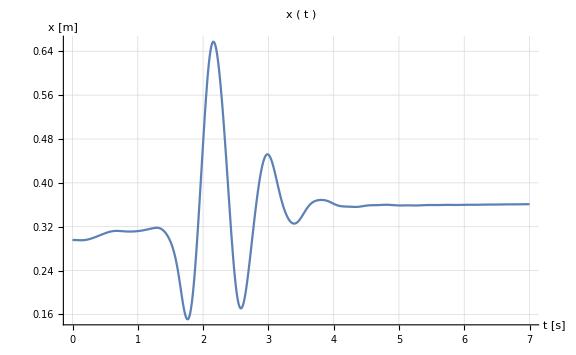
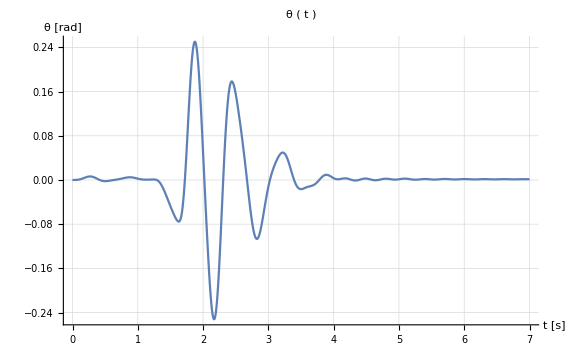

```mathematica
eqs=(𝕖[t]/.{m->125,g->9.8,L->1,k->3000,b->266,
udir[t_]->Piecewise[{{(dz[t]+Sin[angle[t]]),t≤7},{(dz[7]+Sin[angle[7]]),7≤t}}], udir'[t_]->Piecewise[{{(vz[t]+omega[t]),t≤7},{0,7≤t}}], hudir[t_]->Piecewise[{{(1-Cos[angle[t]]),t≤7},{(1-Cos[angle[7]]),7≤t}}], 
hudir'[t_]->Piecewise[{{(0),t≤7},{0,7≤t}}],uesq[t_]->Piecewise[{{(dz[t]-Sin[angle[t]]),t≤7},{(dz[7]-Sin[angle[7]]),7≤t}}], uesq'[t_]->Piecewise[{{(vz[t]-omega[t]),t≤7},{0,7≤t}}],huesq[t_]->Piecewise[{{(1-Cos[angle[t]]),t≤7},{(1-Cos[angle[7]]),7≤t}}], 
huesq'[t_]->Piecewise[{{(0),t≤7},{0,7≤t}}]})/.Rule->Equal;
Module[{sol, ts=7}, sol= NDSolve[Join[eqs, {x[0]==(x[t]/.xeq), θ[0]==0 , x'[0]==0, θ'[0]==0}],{x,θ},{t,0,ts}];
{Plot[ Evaluate[(x[t]/.sol)],{t,0,ts}, PlotRange->All, ImageSize->Large, PlotLabel->"x ( t )", LabelStyle->"Subsection",GridLines->Automatic, AxesLabel->{"t [s]","x [m]"}],
Plot[ Evaluate[(θ[t]/.sol)],{t,0,ts}, PlotRange->All, ImageSize->Large, PlotLabel->"θ ( t )", LabelStyle->"Subsection",GridLines->Automatic, AxesLabel->{"t [s]","θ [rad]"}]
}
]
```